```mathematica
<<VectorAnalysis`
FrameFormat="{Frame→True,ImageSize→450,LabelStyle→Directive[Black,Bold,FontSize→13]}";
```

## General transformation of inclined spherical coordinates

Define Xe,Ye,Ze as coord defind respect to the earth equator plane. Xs, Ys, Zs as sun elllipic. Xp,Yp,Zp as sattelite;

 θ_es is earth inclination angle=23.5 degree,  θ_isat is sattlite inclination angle.  ψ is “Right ascension of the ascending node (RAAN)” . θ_re is the sun’s revolution angle respect to earth center

```mathematica
{Xs,Ys,Zs}=({Xe,Ye,Ze}.TransformationMatrix[RotationTransform[(Subscript[θ, es]),{1,0,0}]][[1;;3,1;;3]]).TransformationMatrix[RotationTransform[(Subscript[θ, re]),{0,0,1}]][[1;;3,1;;3]]
(*express sun coord as earth coord*)
```

{Xe Cos[θ_re]+(Ye Cos[θ_es]+Ze Sin[θ_es]) Sin[θ_re],Cos[θ_re] (Ye Cos[θ_es]+Ze Sin[θ_es])-Xe Sin[θ_re],Ze Cos[θ_es]-Ye Sin[θ_es]}

```mathematica
{XP,YP,ZP}=({Xe,Ye,Ze}.TransformationMatrix[RotationTransform[(ψ),{0,0,1}]][[1;;3,1;;3]]).TransformationMatrix[RotationTransform[(Subscript[θ, isat]),{1,0,0}]][[1;;3,1;;3]]
(*express sattlite coord as earth coord*)
```

{Xe Cos[ψ]+Ye Sin[ψ],Cos[θ_isat] (Ye Cos[ψ]-Xe Sin[ψ])+Ze Sin[θ_isat],Ze Cos[θ_isat]-(Ye Cos[ψ]-Xe Sin[ψ]) Sin[θ_isat]}

```mathematica
pXYZasSpher=Table[{xp,yp,zp}[[i]]->CoordinatesToCartesian[{rp,θp,ϕp},Spherical][[i]],{i,3}]
```

{xp→rp Cos[ϕp] Sin[θp],yp→rp Sin[θp] Sin[ϕp],zp→rp Cos[θp]}

```mathematica
eXYZtoPSub=(Solve[{xp==XP,yp==YP,zp==ZP}/.{Xe->xe,Ye->ye,Ze->ze},{xe,ye,ze}]//FullSimplify)[[1]] (*express earth coord as sattilite coord*)
```

{xe→xp Cos[ψ]+Sin[ψ] (-yp Cos[θ_isat]+zp Sin[θ_isat]),ye→Sin[ψ] (xp+yp Cos[θ_isat] Cot[ψ]-zp Cot[ψ] Sin[θ_isat]),ze→zp Cos[θ_isat]+yp Sin[θ_isat]}

```mathematica
sXYZtoPSub={xs->Xs,ys->Ys,zs->Zs}/.{Xe->xe,Ye->ye,Ze->ze}/.eXYZtoPSub//FullSimplify
(*express elliptic (sun) coord coord as sattilite coord*)
```

{xs→Cos[θ_re] (xp Cos[ψ]+Sin[ψ] (-yp Cos[θ_isat]+zp Sin[θ_isat]))+(Sin[θ_es] (zp Cos[θ_isat]+yp Sin[θ_isat])+Cos[θ_es] Sin[ψ] (xp+yp Cos[θ_isat] Cot[ψ]-zp Cot[ψ] Sin[θ_isat])) Sin[θ_re],ys→Cos[θ_re] (Sin[θ_es] (zp Cos[θ_isat]+yp Sin[θ_isat])+Cos[θ_es] Sin[ψ] (xp+yp Cos[θ_isat] Cot[ψ]-zp Cot[ψ] Sin[θ_isat]))-(xp Cos[ψ]+Sin[ψ] (-yp Cos[θ_isat]+zp Sin[θ_isat])) Sin[θ_re],zs→Cos[θ_es] (zp Cos[θ_isat]+yp Sin[θ_isat])-Sin[ψ] Sin[θ_es] (xp+yp Cos[θ_isat] Cot[ψ]-zp Cot[ψ] Sin[θ_isat])}

```mathematica
erθϕSub=FullSimplify[CoordinatesFromCartesian[{xe,ye,ze},Spherical]/.eXYZtoPSub/.pXYZasSpher,Assumptions->rp>0]   
(*express earth spherical coord as sattilite spherical coord*)
```

{rp,ArcCos[Cos[θp] Cos[θ_isat]+Sin[θp] Sin[ϕp] Sin[θ_isat]],ArcTan[Cos[ϕp] Cos[ψ] Sin[θp]-Cos[θ_isat] Sin[θp] Sin[ϕp] Sin[ψ]+Cos[θp] Sin[ψ] Sin[θ_isat],Cos[ψ] Cos[θ_isat] Sin[θp] Sin[ϕp]+Cos[ϕp] Sin[θp] Sin[ψ]-Cos[θp] Cos[ψ] Sin[θ_isat]]}

To save computation time, I paste the simpflied result below:

```mathematica
srθϕSub={rp,ArcCos[Sin[θp] (-(Cos[ψ] Cos[Subscript[θ, isat]] Sin[ϕp]+Cos[ϕp] Sin[ψ]) Sin[Subscript[θ, es]]+Cos[Subscript[θ, es]] Sin[ϕp] Sin[Subscript[θ, isat]])+Cos[θp] (Cos[Subscript[θ, es]] Cos[Subscript[θ, isat]]+Cos[ψ] Sin[Subscript[θ, es]] Sin[Subscript[θ, isat]])],ArcTan[rp Cos[Subscript[θ, re]] (Cos[ϕp] Cos[ψ] Sin[θp]+Sin[ψ] (-Cos[Subscript[θ, isat]] Sin[θp] Sin[ϕp]+Cos[θp] Sin[Subscript[θ, isat]]))+(rp Cos[Subscript[θ, es]] Sin[ψ] (Sin[θp] (Cos[ϕp]+Cos[Subscript[θ, isat]] Cot[ψ] Sin[ϕp])-Cos[θp] Cot[ψ] Sin[Subscript[θ, isat]])+rp Sin[Subscript[θ, es]] (Cos[θp] Cos[Subscript[θ, isat]]+Sin[θp] Sin[ϕp] Sin[Subscript[θ, isat]])) Sin[Subscript[θ, re]],Cos[Subscript[θ, re]] (rp Cos[Subscript[θ, es]] Sin[ψ] (Sin[θp] (Cos[ϕp]+Cos[Subscript[θ, isat]] Cot[ψ] Sin[ϕp])-Cos[θp] Cot[ψ] Sin[Subscript[θ, isat]])+rp Sin[Subscript[θ, es]] (Cos[θp] Cos[Subscript[θ, isat]]+Sin[θp] Sin[ϕp] Sin[Subscript[θ, isat]]))-rp (Cos[ϕp] Cos[ψ] Sin[θp]+Sin[ψ] (-Cos[Subscript[θ, isat]] Sin[θp] Sin[ϕp]+Cos[θp] Sin[Subscript[θ, isat]])) Sin[Subscript[θ, re]]]};
```

## Sattelite orbit analysis

```mathematica
θEorbit[θisatv_,ϕpv_,ψv_,θrev_]:=erθϕSub[[2]]/.{θp->Pi/2,ϕp->ϕpv,ψ->ψv,Subscript[θ, isat]->θisatv,Subscript[θ, re]->θrev}
ϕEorbit[θisatv_,ϕpv_,ψv_,θrev_]:=erθϕSub[[3]]/.{θp->Pi/2,ϕp->ϕpv,ψ->ψv,Subscript[θ, isat]->θisatv,Subscript[θ, re]->θrev}
(*spherical coordinate of moving sattllite respect to earth equatorial plane, Pi/2 minus θEorbit will represent the lattidude, while ϕEorbit is the longitude *)
```

```mathematica
DegToRad[x_]:=x/180*Pi
Rad2degree[x_]:=x/Pi*180;
```

```mathematica
θorbit[θisatv_,ϕpv_,ψv_,θrev_]:=srθϕSub[[2]]/.{θp->Pi/2,ϕp->ϕpv,Subscript[θ, es]->DegToRad[23.5],ψ->ψv,Subscript[θ, isat]->θisatv,Subscript[θ, re]->θrev}
ϕorbit[θisatv_,ϕpv_,ψv_,θrev_]:=srθϕSub[[3]]/.{θp->Pi/2,ϕp->ϕpv,Subscript[θ, es]->DegToRad[23.5],ψ->ψv,Subscript[θ, isat]->θisatv,Subscript[θ, re]->θrev}
(*spherical coordinate of moving sattllite respect to ecliptic plane, i.e. ecliptic plane as the x-y plane. 
Here Subscript[θ, inc] is the inclination angle of the satellite orbit respect to ecliptic plane: Subscript[θ, inc]=θi[sat]-θi[es], where
θi[sat] is the incliation angle of satellite respect to earth equatorial plane,
θi[es] is inclination angle of earth rotationa axis respect to the normal vector of ecliptic plane
*)
```

```mathematica
T=1 ;
w=2Pi/T ;(*augular velocity of the sattelite*)
```

```mathematica
wre=2Pi/(T*Ntot); Ntot=Round[(365*24*60)/Ts];
  (*wre is the angular velocity of sun respect to earth center, Ntot is number of sattllite period over a year;Ts is the explicit value of one sattilite period in minuites*)
```

Track the sattelite’s moving trajectory

```mathematica
θt[θisat_,t_,ψv_]:=θorbit[θisat,w*t,ψv,wre*t]
ϕt[θisat_,t_,ψv_]:=ϕorbit[θisat,w*t,ψv,wre*t]
```

```mathematica
θEt[θisat_,t_,ψv_]:=θEorbit[θisat,w*t,ψv,wre*t]
ϕEt[θisat_,t_,ψv_]:=ϕEorbit[θisat,w*t,ψv,wre*t]
```

## Shadow analysis

-Graphics- -Graphics-

define α =angle beween r⃗ (vector from earth center to satllite) and OA2
then from trig relations we have Cos[α]=y/r=Sin[θ]Sin[ϕ], where θ,ϕ are defined in the coord system where the ecliptic plane as the x-y plane (see left graph above), and OA2 as y axis.
On the other hand, define α_c to be the point of intersection beween sattle orbit and earth shadow
"U" to be the open angle of Umbra cone (darkest color in the right graph above),

```mathematica
A2B2=Sqrt[r^2+OA2^2-2*r*OA2*Cosα];
CosU=(OA2^2+A2B2^2-r^2)/(2*A2B2*OA2);
Solve[Cos[U]==CosU,Cosα];
{Cosαc1,Cosαc2}=Cosα/.FullSimplify[%]; (*Obtained αc as functions of angle U, OA2, and sattlite radial distance r=R+L*)
```

```mathematica
km=1;
subPara={Rearth->6400km, Rsun->696340km,OP->1.48*10^8 km,r->(L+6400)km,rp->(L+6400)km};
U=ArcSin[( Rsun-Rearth)/OP/.subPara];
Rad2degree[U];
OA2=Rearth/Sin[U]/.subPara;
```

```mathematica
αc[Lv_]:=ArcCos[Cosαc2/.subPara/.L->Lv]
```

Thus we obtain value of αc=65.8374 dgree for a sattelite of height=600km

```mathematica
αt[θisat_,t_,ψv_]:=FullSimplify[ArcCos[Sin[θt[θisat,t,ψv]]Sin[ϕt[θisat,t,ψv]]]]
```

```mathematica
PhiSelect[x_]:=If[x<0,x+360,If[x>=360,x-360,x]]
```

## Example: Suzaku satellite (low inclination angle)

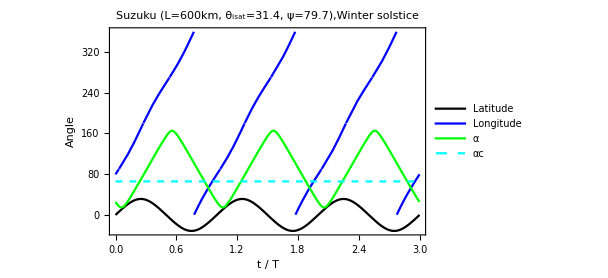

```mathematica
L=600;θisat=DegToRad[31.38];ψv=DegToRad[79.725];Ti=0T;Tf=Ti+3T;
Ts=96;
Show[Plot[{Rad2degree[Pi/2-θEt[θisat,t,ψv]],PhiSelect[Rad2degree[ϕEt[θisat,t,ψv]]],Rad2degree[αt[θisat,t,ψv]/.subPara]},{t,Ti,Tf},PlotStyle->{Black,Blue,Green},PlotLegends->{"Latitude","Longitude","α"}],
Plot[Rad2degree[αc[L]],{t,Ti,Tf},PlotStyle->{Cyan,Dashed},PlotLegends->{"αc"}],ToExpression[FrameFormat],FrameLabel->{"t / T","Angle"},PlotLabel->"Suzuku (L=600km, θ_isat=31.4, ψ=79.7),Winter solstice"]
```

The satellite is in earth’s dark side (shadow)  when α<αc

```mathematica
ShadowT[t_]:= If[FullSimplify[(αt[θisat,t,ψv]/.subPara)-αc[L]]≤0,1,0]
```

Calculate the fraction of a year when the satellite is in shadow